```mathematica
allGeneratorVariables=Sort[Table[
With[
{sets=ConnectedComponents[ GraphComplement[allGraphs5[k,"graph"]]]},
allGraphs5[k,"colofourgenerator"]=PartitionToSymbol[sets,"g"]
],
{k,allGraphs5GeneratorAtomKeys}
],CompareSymbols]
```

{g1x2x3x4x5,g1x2x3x45,g1x2x34x5,g1x2x35x4,g1x23x4x5,g1x24x3x5,g1x25x3x4,g12x3x4x5,g13x2x4x5,g14x2x3x5,g15x2x3x4,g1x23x45,g1x24x35,g1x25x34,g12x3x45,g12x34x5,g12x35x4,g13x2x45,g13x24x5,g13x25x4,g14x2x35,g14x23x5,g14x25x3,g15x2x34,g15x23x4,g15x24x3,g1x2x345,g1x234x5,g1x235x4,g1x245x3,g123x4x5,g124x3x5,g125x3x4,g134x2x5,g135x2x4,g145x2x3,g12x345,g123x45,g124x35,g125x34,g13x245,g134x25,g135x24,g14x235,g145x23,g15x234,g1x2345,g1234x5,g1235x4,g1245x3,g1345x2,g12345}

```mathematica
repFullToGen=ToRules[
Reduce[
Table[
allGraphs5[k,"colofourgenerator"]==allGraphs5[k,"colofour"]
,
{k,allGraphs5GeneratorAtomKeys}
],
Table[allGraphs5[k,"colofour"],{k,allGraphs5AtomKeys}]
]
];
```

```mathematica
Monitor[
Table[
allGraphs5[k,"colofourgenerator"]=Simplify[allGraphs5[k,"colofour"]/.repFullToGen],
{k,Sort[Keys[allGraphs5]]}
],k]
```

{g12345,1893,g12345-g1234x5-g1235x4-g123x45+2 g123x4x5-g1245x3-g124x35+2 g124x3x5-g125x34+2 g125x3x4-g12x345+2 g12x34x5+2 g12x35x4+2 g12x3x45-6 g12x3x4x5-g1345x2-g134x25+2 g134x2x5-g135x24+2 g135x2x4-g13x245+2 g13x24x5+2 g13x25x4+2 g13x2x45-6 g13x2x4x5-g145x23+2 g145x2x3-g14x235+2 g14x23x5+2 g14x25x3+2 g14x2x35-6 g14x2x3x5-g15x234+2 g15x23x4+2 g15x24x3+2 g15x2x34-6 g15x2x3x4-g1x2345+2 g1x234x5+2 g1x235x4+2 g1x23x45-6 g1x23x4x5+2 g1x245x3+2 g1x24x35-6 g1x24x3x5+2 g1x25x34-6 g1x25x3x4+2 g1x2x345-6 g1x2x34x5-6 g1x2x35x4-6 g1x2x3x45+24 g1x2x3x4x5}
 |  |  |  |

```mathematica
repGenerators=Table[
allGraphs5[k,"colofourgenerator"]->Labeled[ShowGraph5Least[k],SymbolToLabel[allGraphs5[k,"colofourgenerator"]]]
,
{k,allGraphs5GeneratorAtomKeys}
];
```

```mathematica
TableForm[Table[ShowGraph5Least[k]->(allGraphs5[k,"colofourgenerator"]/.repGenerators),{k,alfa1s}]]
```

-Graphics-361660→-Graphics-22882013♁24♁5--Graphics-2944301♁24♁3♁5--Graphics-22963013♁2♁4♁5+-Graphics-2952401♁2♁3♁4♁5
-Graphics-317380→-Graphics-27310014♁25♁3--Graphics-2949701♁25♁3♁4--Graphics-27337014♁2♁3♁5+-Graphics-2952401♁2♁3♁4♁5
-Graphics-296080→-Graphics-2944001♁24♁35--Graphics-2952101♁2♁35♁4--Graphics-2944301♁24♁3♁5+-Graphics-2952401♁2♁3♁4♁5
-Graphics-361120→-Graphics-22936013♁25♁4--Graphics-2949701♁25♁3♁4--Graphics-22963013♁2♁4♁5+-Graphics-2952401♁2♁3♁4♁5
-Graphics-317140→-Graphics-27334014♁2♁35--Graphics-2952101♁2♁35♁4--Graphics-27337014♁2♁3♁5+-Graphics-2952401♁2♁3♁4♁5

```mathematica
TableForm[Table[ShowGraph5Least[k]->(allGraphs5[k,"colofourgenerator"]/.repGenerators),{k,quads}]]
```

-Graphics-360850→-Graphics-22963013♁2♁4♁5--Graphics-2952401♁2♁3♁4♁5
-Graphics-296050→-Graphics-2944301♁24♁3♁5--Graphics-2952401♁2♁3♁4♁5
-Graphics-295270→-Graphics-2952101♁2♁35♁4--Graphics-2952401♁2♁3♁4♁5
-Graphics-317110→-Graphics-27337014♁2♁3♁5--Graphics-2952401♁2♁3♁4♁5
-Graphics-295510→-Graphics-2949701♁25♁3♁4--Graphics-2952401♁2♁3♁4♁5

```mathematica
Table[allGraphs5[k,"colofourgenerator"]/.repGenerators,{k,Sort[allGraphs5GeneratorAtomKeys,allGraphs5[#1,"atleast"]>allGraphs5[#2,"atleast"]&]}]
```

{-Graphics-03412345,-Graphics-2003481345♁2,-Graphics-681681245♁3,-Graphics-227881235♁4,-Graphics-76081234♁5,-Graphics-2916081♁2345,-Graphics-28462515♁234,-Graphics-263645145♁23,-Graphics-90765125♁34,-Graphics-30365123♁45,-Graphics-9828512♁345,-Graphics-27064314♁235,-Graphics-221503135♁24,-Graphics-207403134♁25,-Graphics-22854313♁245,-Graphics-75703124♁35,-Graphics-266071145♁2♁3,-Graphics-222311135♁2♁4,-Graphics-207671134♁2♁5,-Graphics-90851125♁3♁4,-Graphics-75731124♁3♁5,-Graphics-30371123♁4♁5,-Graphics-2941511♁245♁3,-Graphics-2925111♁235♁4,-Graphics-2919111♁234♁5,-Graphics-2951111♁2♁345,-Graphics-28714115♁24♁3,-Graphics-28552115♁23♁4,-Graphics-28786115♁2♁34,-Graphics-27094114♁23♁5,-Graphics-22962113♁2♁45,-Graphics-9838112♁35♁4,-Graphics-9832112♁34♁5,-Graphics-9840112♁3♁45,-Graphics-2948811♁25♁34,-Graphics-2928011♁23♁45,-Graphics-27310014♁25♁3,-Graphics-27334014♁2♁35,-Graphics-22936013♁25♁4,-Graphics-22882013♁24♁5,-Graphics-2944001♁24♁35,-Graphics-28795015♁2♁3♁4,-Graphics-27337014♁2♁3♁5,-Graphics-22963013♁2♁4♁5,-Graphics-9841012♁3♁4♁5,-Graphics-2949701♁25♁3♁4,-Graphics-2944301♁24♁3♁5,-Graphics-2928101♁23♁4♁5,-Graphics-2952101♁2♁35♁4,-Graphics-2951501♁2♁34♁5,-Graphics-2952301♁2♁3♁45,-Graphics-2952401♁2♁3♁4♁5}

```mathematica
TableForm[Table[ShowGraph5Least[k]->(allGraphs5[k,"colofourgenerator"]/.repGenerators),{k,{lambdaKey,alfaKey}}]]
```

-Graphics-206653→-Graphics-2944001♁24♁35+-Graphics-27334014♁2♁35+-Graphics-27310014♁25♁3+-Graphics-22936013♁25♁4+-Graphics-22882013♁24♁5--Graphics-2952101♁2♁35♁4--Graphics-2949701♁25♁3♁4--Graphics-2944301♁24♁3♁5--Graphics-27337014♁2♁3♁5--Graphics-22963013♁2♁4♁5+-Graphics-2952401♁2♁3♁4♁5
-Graphics-359771→-Graphics-22936013♁25♁4+-Graphics-22882013♁24♁5--Graphics-2949701♁25♁3♁4--Graphics-2944301♁24♁3♁5--Graphics-22963013♁2♁4♁5+-Graphics-2952401♁2♁3♁4♁5

```mathematica
GenCoeff[poly_]:=Table[Coefficient[poly,x],{x,allGeneratorVariables}]
```

```mathematica
allEmptyVariables=Sort[Table[
allGraphs5[k,"colofourrealnull"],
{k,allGraphs5NullAtomKeys}
],CompareSymbols]
```

{n1x2x3x4x5,n1x2x3x45,n1x2x34x5,n1x2x35x4,n1x23x4x5,n1x24x3x5,n1x25x3x4,n12x3x4x5,n13x2x4x5,n14x2x3x5,n15x2x3x4,n1x23x45,n1x24x35,n1x25x34,n12x3x45,n12x34x5,n12x35x4,n13x2x45,n13x24x5,n13x25x4,n14x2x35,n14x23x5,n14x25x3,n15x2x34,n15x23x4,n15x24x3,n1x2x345,n1x234x5,n1x235x4,n1x245x3,n123x4x5,n124x3x5,n125x3x4,n134x2x5,n135x2x4,n145x2x3,n12x345,n123x45,n124x35,n125x34,n13x245,n134x25,n135x24,n14x235,n145x23,n15x234,n1x2345,n1234x5,n1235x4,n1245x3,n1345x2,n12345}

```mathematica
allFullVariables=Table[PartitionType[ SymbolToSets[k]],{k,allGeneratorVariables}]
```

{{1,1,1,1,1},{2,1,1,1},{2,1,1,1},{2,1,1,1},{2,1,1,1},{2,1,1,1},{2,1,1,1},{2,1,1,1},{2,1,1,1},{2,1,1,1},{2,1,1,1},{2,2,1},{2,2,1},{2,2,1},{2,2,1},{2,2,1},{2,2,1},{2,2,1},{2,2,1},{2,2,1},{2,2,1},{2,2,1},{2,2,1},{2,2,1},{2,2,1},{2,2,1},{3,1,1},{3,1,1},{3,1,1},{3,1,1},{3,1,1},{3,1,1},{3,1,1},{3,1,1},{3,1,1},{3,1,1},{3,2},{3,2},{3,2},{3,2},{3,2},{3,2},{3,2},{3,2},{3,2},{3,2},{4,1},{4,1},{4,1},{4,1},{4,1},{5}}

```mathematica
EmptyCoeff[poly_]:=Table[Coefficient[poly,x],{x,allEmptyVariables}]
```

```mathematica
GenCoeff[allGraphs5[alfa1Key,"colofourgenerator"]]
```

{1,0,0,0,0,-1,0,0,-1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
NoZero[k_]:=If[k==0,"",k]
```

```mathematica
MatrixForm[Table[Map[NoZero,GenCoeff[allGraphs5[k,"colofourgenerator"]]],{k,alfa1s}],TableHeadings->{alfa1s,Table[Rotate[SymbolToLabel[k],Pi/2],{k,allGeneratorVariables}]}]
```

( | 1♁2♁3♁4♁5 | 1♁2♁3♁45 | 1♁2♁34♁5 | 1♁2♁35♁4 | 1♁23♁4♁5 | 1♁24♁3♁5 | 1♁25♁3♁4 | 12♁3♁4♁5 | 13♁2♁4♁5 | 14♁2♁3♁5 | 15♁2♁3♁4 | 1♁23♁45 | 1♁24♁35 | 1♁25♁34 | 12♁3♁45 | 12♁34♁5 | 12♁35♁4 | 13♁2♁45 | 13♁24♁5 | 13♁25♁4 | 14♁2♁35 | 14♁23♁5 | 14♁25♁3 | 15♁2♁34 | 15♁23♁4 | 15♁24♁3 | 1♁2♁345 | 1♁234♁5 | 1♁235♁4 | 1♁245♁3 | 123♁4♁5 | 124♁3♁5 | 125♁3♁4 | 134♁2♁5 | 135♁2♁4 | 145♁2♁3 | 12♁345 | 123♁45 | 124♁35 | 125♁34 | 13♁245 | 134♁25 | 135♁24 | 14♁235 | 145♁23 | 15♁234 | 1♁2345 | 1234♁5 | 1235♁4 | 1245♁3 | 1345♁2 | 12345
36166 | 1 |  |  |  |  | -1 |  |  | -1 |  |  |  |  |  |  |  |  |  | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
31738 | 1 |  |  |  |  |  | -1 |  |  | -1 |  |  |  |  |  |  |  |  |  |  |  |  | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
29608 | 1 |  |  | -1 |  | -1 |  |  |  |  |  |  | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
36112 | 1 |  |  |  |  |  | -1 |  | -1 |  |  |  |  |  |  |  |  |  |  | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
31714 | 1 |  |  | -1 |  |  |  |  |  | -1 |  |  |  |  |  |  |  |  |  |  | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | )

```mathematica
MatrixForm[Table[Map[NoZero,GenCoeff[allGraphs5[k,"colofourgenerator"]]],{k,quads}],TableHeadings->{quads,Table[Rotate[SymbolToLabel[k],Pi/2],{k,allGeneratorVariables}]}]
```

( | 1♁2♁3♁4♁5 | 1♁2♁3♁45 | 1♁2♁34♁5 | 1♁2♁35♁4 | 1♁23♁4♁5 | 1♁24♁3♁5 | 1♁25♁3♁4 | 12♁3♁4♁5 | 13♁2♁4♁5 | 14♁2♁3♁5 | 15♁2♁3♁4 | 1♁23♁45 | 1♁24♁35 | 1♁25♁34 | 12♁3♁45 | 12♁34♁5 | 12♁35♁4 | 13♁2♁45 | 13♁24♁5 | 13♁25♁4 | 14♁2♁35 | 14♁23♁5 | 14♁25♁3 | 15♁2♁34 | 15♁23♁4 | 15♁24♁3 | 1♁2♁345 | 1♁234♁5 | 1♁235♁4 | 1♁245♁3 | 123♁4♁5 | 124♁3♁5 | 125♁3♁4 | 134♁2♁5 | 135♁2♁4 | 145♁2♁3 | 12♁345 | 123♁45 | 124♁35 | 125♁34 | 13♁245 | 134♁25 | 135♁24 | 14♁235 | 145♁23 | 15♁234 | 1♁2345 | 1234♁5 | 1235♁4 | 1245♁3 | 1345♁2 | 12345
36085 | -1 |  |  |  |  |  |  |  | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
29605 | -1 |  |  |  |  | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
29527 | -1 |  |  | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
31711 | -1 |  |  |  |  |  |  |  |  | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
29551 | -1 |  |  |  |  |  | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | )

```mathematica
MatrixForm[Table[Map[NoZero,EmptyCoeff[allGraphs5[k,"colofourrealnull"]]],{k,alfa1s}],TableHeadings->{alfa1s,Table[Rotate[SymbolToLabel[k],Pi/2],{k,allEmptyVariables}]}]
```

( | 1♁2♁3♁4♁5 | 1♁2♁3♁45 | 1♁2♁34♁5 | 1♁2♁35♁4 | 1♁23♁4♁5 | 1♁24♁3♁5 | 1♁25♁3♁4 | 12♁3♁4♁5 | 13♁2♁4♁5 | 14♁2♁3♁5 | 15♁2♁3♁4 | 1♁23♁45 | 1♁24♁35 | 1♁25♁34 | 12♁3♁45 | 12♁34♁5 | 12♁35♁4 | 13♁2♁45 | 13♁24♁5 | 13♁25♁4 | 14♁2♁35 | 14♁23♁5 | 14♁25♁3 | 15♁2♁34 | 15♁23♁4 | 15♁24♁3 | 1♁2♁345 | 1♁234♁5 | 1♁235♁4 | 1♁245♁3 | 123♁4♁5 | 124♁3♁5 | 125♁3♁4 | 134♁2♁5 | 135♁2♁4 | 145♁2♁3 | 12♁345 | 123♁45 | 124♁35 | 125♁34 | 13♁245 | 134♁25 | 135♁24 | 14♁235 | 145♁23 | 15♁234 | 1♁2345 | 1234♁5 | 1235♁4 | 1245♁3 | 1345♁2 | 12345
36166 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | -1 |  | -1 |  |  |  |  | -1 |  |  |  | 2
31738 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | -1 |  | -1 |  |  |  |  |  | -1 |  | 2
29608 |  |  |  |  |  |  |  |  |  |  |  |  | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | -1 |  |  |  | -1 |  |  |  | -1 |  |  |  |  | 2
36112 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | -1 | -1 |  |  |  |  |  |  | -1 |  |  | 2
31714 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | -1 |  |  |  |  | -1 |  |  |  |  |  |  | -1 | 2)

```mathematica
MatrixForm[Table[Map[NoZero,EmptyCoeff[allGraphs5[k,"colofourrealnull"]]],{k,quads}],TableHeadings->{quads,Table[Rotate[SymbolToLabel[k],Pi/2],{k,allEmptyVariables}]}]
```

( | 1♁2♁3♁4♁5 | 1♁2♁3♁45 | 1♁2♁34♁5 | 1♁2♁35♁4 | 1♁23♁4♁5 | 1♁24♁3♁5 | 1♁25♁3♁4 | 12♁3♁4♁5 | 13♁2♁4♁5 | 14♁2♁3♁5 | 15♁2♁3♁4 | 1♁23♁45 | 1♁24♁35 | 1♁25♁34 | 12♁3♁45 | 12♁34♁5 | 12♁35♁4 | 13♁2♁45 | 13♁24♁5 | 13♁25♁4 | 14♁2♁35 | 14♁23♁5 | 14♁25♁3 | 15♁2♁34 | 15♁23♁4 | 15♁24♁3 | 1♁2♁345 | 1♁234♁5 | 1♁235♁4 | 1♁245♁3 | 123♁4♁5 | 124♁3♁5 | 125♁3♁4 | 134♁2♁5 | 135♁2♁4 | 145♁2♁3 | 12♁345 | 123♁45 | 124♁35 | 125♁34 | 13♁245 | 134♁25 | 135♁24 | 14♁235 | 145♁23 | 15♁234 | 1♁2345 | 1234♁5 | 1235♁4 | 1245♁3 | 1345♁2 | 12345
36085 |  |  |  |  |  |  |  |  | 1 |  |  |  |  |  |  |  |  | -1 | -1 | -1 |  |  |  |  |  |  |  |  |  |  | -1 |  |  | -1 | -1 |  |  | 1 |  |  | 2 | 1 | 1 |  |  |  |  | 2 | 2 |  | 2 | -6
29605 |  |  |  |  |  | 1 |  |  |  |  |  |  | -1 |  |  |  |  |  | -1 |  |  |  |  |  |  | -1 |  | -1 |  | -1 |  | -1 |  |  |  |  |  |  | 1 |  | 1 |  | 2 |  |  | 1 | 2 | 2 |  | 2 |  | -6
29527 |  |  |  | 1 |  |  |  |  |  |  |  |  | -1 |  |  |  | -1 |  |  |  | -1 |  |  |  |  |  | -1 |  | -1 |  |  |  |  |  | -1 |  | 1 |  | 2 |  |  |  | 1 | 1 |  |  | 2 |  | 2 |  | 2 | -6
31711 |  |  |  |  |  |  |  |  |  | 1 |  |  |  |  |  |  |  |  |  |  | -1 | -1 | -1 |  |  |  |  |  |  |  |  | -1 |  | -1 |  | -1 |  |  | 1 |  |  | 1 |  | 2 | 1 |  |  | 2 |  | 2 | 2 | -6
29551 |  |  |  |  |  |  | 1 |  |  |  |  |  |  | -1 |  |  |  |  |  | -1 |  |  | -1 |  |  |  |  |  | -1 | -1 |  |  | -1 |  |  |  |  |  |  | 1 | 1 | 2 |  | 1 |  |  | 2 |  | 2 | 2 |  | -6)

```mathematica
MatrixForm[Map[NoZero,GenCoeff[Total[Table[allGraphs5[k,"colofourgenerator"],{k,quads}] ]]],TableHeadings->{Table[Rotate[SymbolToLabel[k],Pi/2],{k,allEmptyVariables}],Table[Rotate[SymbolToLabel[k],Pi/2],{k,allEmptyVariables}]}, TableDirections->Row]
```

(1♁2♁3♁4♁5 | 1♁2♁3♁45 | 1♁2♁34♁5 | 1♁2♁35♁4 | 1♁23♁4♁5 | 1♁24♁3♁5 | 1♁25♁3♁4 | 12♁3♁4♁5 | 13♁2♁4♁5 | 14♁2♁3♁5 | 15♁2♁3♁4 | 1♁23♁45 | 1♁24♁35 | 1♁25♁34 | 12♁3♁45 | 12♁34♁5 | 12♁35♁4 | 13♁2♁45 | 13♁24♁5 | 13♁25♁4 | 14♁2♁35 | 14♁23♁5 | 14♁25♁3 | 15♁2♁34 | 15♁23♁4 | 15♁24♁3 | 1♁2♁345 | 1♁234♁5 | 1♁235♁4 | 1♁245♁3 | 123♁4♁5 | 124♁3♁5 | 125♁3♁4 | 134♁2♁5 | 135♁2♁4 | 145♁2♁3 | 12♁345 | 123♁45 | 124♁35 | 125♁34 | 13♁245 | 134♁25 | 135♁24 | 14♁235 | 145♁23 | 15♁234 | 1♁2345 | 1234♁5 | 1235♁4 | 1245♁3 | 1345♁2 | 12345
-5 |  |  | 1 |  | 1 | 1 |  | 1 | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | )

```mathematica
MatrixForm[Map[NoZero,GenCoeff[Total[Table[allGraphs5[k,"colofourgenerator"],{k,alfa1s}] ]]],TableHeadings->{Table[Rotate[SymbolToLabel[k],Pi/2],{k,allEmptyVariables}],Table[Rotate[SymbolToLabel[k],Pi/2],{k,allEmptyVariables}]}, TableDirections->Row]
```

(1♁2♁3♁4♁5 | 1♁2♁3♁45 | 1♁2♁34♁5 | 1♁2♁35♁4 | 1♁23♁4♁5 | 1♁24♁3♁5 | 1♁25♁3♁4 | 12♁3♁4♁5 | 13♁2♁4♁5 | 14♁2♁3♁5 | 15♁2♁3♁4 | 1♁23♁45 | 1♁24♁35 | 1♁25♁34 | 12♁3♁45 | 12♁34♁5 | 12♁35♁4 | 13♁2♁45 | 13♁24♁5 | 13♁25♁4 | 14♁2♁35 | 14♁23♁5 | 14♁25♁3 | 15♁2♁34 | 15♁23♁4 | 15♁24♁3 | 1♁2♁345 | 1♁234♁5 | 1♁235♁4 | 1♁245♁3 | 123♁4♁5 | 124♁3♁5 | 125♁3♁4 | 134♁2♁5 | 135♁2♁4 | 145♁2♁3 | 12♁345 | 123♁45 | 124♁35 | 125♁34 | 13♁245 | 134♁25 | 135♁24 | 14♁235 | 145♁23 | 15♁234 | 1♁2345 | 1234♁5 | 1235♁4 | 1245♁3 | 1345♁2 | 12345
5 |  |  | -2 |  | -2 | -2 |  | -2 | -2 |  |  | 1 |  |  |  |  |  | 1 | 1 | 1 |  | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | )

```mathematica
Total[Table[allGraphs5[k,"colofourgenerator"],{k,quads}]]/.repGenerators
```

-Graphics-2952101♁2♁35♁4+-Graphics-2949701♁25♁3♁4+-Graphics-2944301♁24♁3♁5+-Graphics-27337014♁2♁3♁5+-Graphics-22963013♁2♁4♁5-5 -Graphics-2952401♁2♁3♁4♁5

```mathematica
Total[Table[allGraphs5[k,"colofourgenerator"],{k,alfa1s}]]/.repGenerators
```

-Graphics-2944001♁24♁35+-Graphics-27334014♁2♁35+-Graphics-27310014♁25♁3+-Graphics-22936013♁25♁4+-Graphics-22882013♁24♁5-2 -Graphics-2952101♁2♁35♁4-2 -Graphics-2949701♁25♁3♁4-2 -Graphics-2944301♁24♁3♁5-2 -Graphics-27337014♁2♁3♁5-2 -Graphics-22963013♁2♁4♁5+5 -Graphics-2952401♁2♁3♁4♁5

```mathematica
Total[Table[allGraphs5[k,"colofourgenerator"],{k,Join[alfa1s,quads]}]]/.repGenerators
```

-Graphics-2944001♁24♁35+-Graphics-27334014♁2♁35+-Graphics-27310014♁25♁3+-Graphics-22936013♁25♁4+-Graphics-22882013♁24♁5--Graphics-2952101♁2♁35♁4--Graphics-2949701♁25♁3♁4--Graphics-2944301♁24♁3♁5--Graphics-27337014♁2♁3♁5--Graphics-22963013♁2♁4♁5

```mathematica
Total[Table[allGraphs5[k,"colofourgenerator"],{k,{lambdaKey}}]]/.repGenerators
```

-Graphics-2944001♁24♁35+-Graphics-27334014♁2♁35+-Graphics-27310014♁25♁3+-Graphics-22936013♁25♁4+-Graphics-22882013♁24♁5--Graphics-2952101♁2♁35♁4--Graphics-2949701♁25♁3♁4--Graphics-2944301♁24♁3♁5--Graphics-27337014♁2♁3♁5--Graphics-22963013♁2♁4♁5+-Graphics-2952401♁2♁3♁4♁5

```mathematica
Det[Table[GenCoeff[allGraphs5[k,"colofourgenerator"]],{k,allGraphs5FakeAtomKeys}]]
```

-195689447424

```mathematica
Det[Table[GenCoeff[allGraphs5[k,"colofourgenerator"]],{k,allGraphs5AtomKeys}]//Inverse]
```

-1

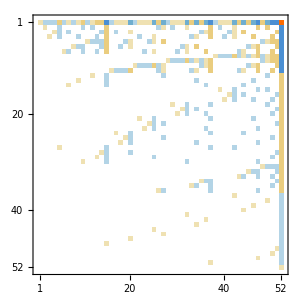

```mathematica
MatrixPlot[Table[GenCoeff[allGraphs5[k,"colofourgenerator"]],{k,allGraphs5AtomKeys}]//Transpose,ImageSize->300]
```

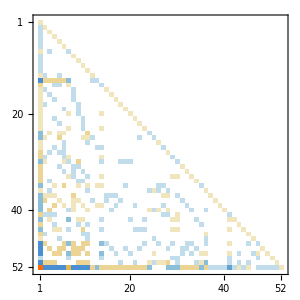

```mathematica
{l,p,c}=LUDecomposition[ Table[GenCoeff[allGraphs5[k,"colofourgenerator"]],{k,allGraphs5AtomKeys}]];matrix1=LowerTriangularize[l];MatrixPlot[matrix1,ImageSize->300]
```

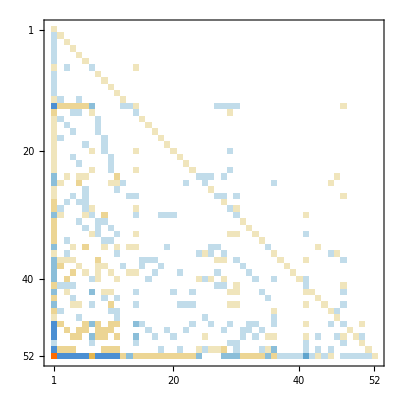

```mathematica
MatrixPlot[l]
```

```mathematica
allFullVariables=Table[allGraphs5[k,"colofour"],{k,allGraphs5AtomKeys}]
```

{v1x2x3x4x5,v1x2x3x45,v1x2x35x4,v1x2x34x5,v1x2x345,v1x25x3x4,v1x25x34,v1x24x3x5,v1x24x35,v1x245x3,v1x23x4x5,v1x23x45,v1x235x4,v1x234x5,v1x2345,v15x2x3x4,v15x2x34,v15x24x3,v15x23x4,v15x234,v14x2x3x5,v14x2x35,v14x25x3,v14x23x5,v14x235,v145x2x3,v145x23,v13x2x4x5,v13x2x45,v13x25x4,v13x24x5,v13x245,v135x2x4,v135x24,v134x2x5,v134x25,v1345x2,v12x3x4x5,v12x3x45,v12x35x4,v12x34x5,v12x345,v125x3x4,v125x34,v124x3x5,v124x35,v1245x3,v123x4x5,v123x45,v1235x4,v1234x5,v12345}

```mathematica
Map[PartitionType[SymbolToSets[#]]&,allFullVariables]
```

{{1,1,1,1,1},{2,1,1,1},{2,1,1,1},{2,1,1,1},{3,1,1},{2,1,1,1},{2,2,1},{2,1,1,1},{2,2,1},{3,1,1},{2,1,1,1},{2,2,1},{3,1,1},{3,1,1},{4,1},{2,1,1,1},{2,2,1},{2,2,1},{2,2,1},{3,2},{2,1,1,1},{2,2,1},{2,2,1},{2,2,1},{3,2},{3,1,1},{3,2},{2,1,1,1},{2,2,1},{2,2,1},{2,2,1},{3,2},{3,1,1},{3,2},{3,1,1},{3,2},{4,1},{2,1,1,1},{2,2,1},{2,2,1},{2,2,1},{3,2},{3,1,1},{3,2},{3,1,1},{3,2},{4,1},{3,1,1},{3,2},{4,1},{4,1},{5}}

```mathematica
Map[PartitionType[SymbolToSets[#]]&,Table[allFullVariables[[p[[k]]]],{k,1,52}]]
```

{{1,1,1,1,1},{2,1,1,1},{2,1,1,1},{2,1,1,1},{2,1,1,1},{2,1,1,1},{2,2,1},{2,1,1,1},{2,1,1,1},{2,1,1,1},{2,1,1,1},{2,2,1},{4,1},{3,1,1},{2,2,1},{2,2,1},{2,2,1},{2,2,1},{2,2,1},{2,2,1},{2,2,1},{2,2,1},{2,2,1},{3,2},{3,2},{2,2,1},{2,2,1},{3,1,1},{3,1,1},{3,2},{3,1,1},{3,1,1},{3,1,1},{3,1,1},{3,2},{2,2,1},{3,2},{3,2},{3,2},{3,2},{3,1,1},{3,2},{3,1,1},{3,2},{3,1,1},{2,2,1},{4,1},{4,1},{4,1},{2,1,1,1},{4,1},{5}}

```mathematica
p
```

{1,2,4,3,11,8,7,38,28,21,16,12,15,13,39,41,40,29,31,30,22,24,23,20,27,18,9,14,10,32,48,45,43,35,34,17,42,49,46,44,5,36,33,25,26,19,47,51,50,6,37,52}

```mathematica
c
```

0

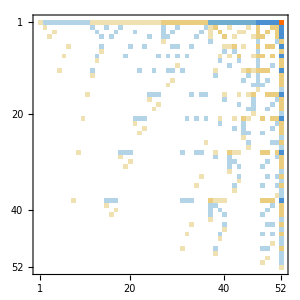

```mathematica
matrix2=Table[EmptyCoeff[allGraphs5[k,"colofourrealnull"]],{k,allGraphs5AtomKeys}];MatrixPlot[matrix2,ImageSize->300]
```

```mathematica
{MatrixPlot[matrix1,ImageSize->300],MatrixPlot[matrix2,ImageSize->300]}
```

{-Graphics-,-Graphics-}

```mathematica
RotateMat[mat_]:=Table[mat[[1+Length[mat]-j,1+Length[mat]-i]],{i,1,Length[mat]},{j,1,Length[mat]}]
```

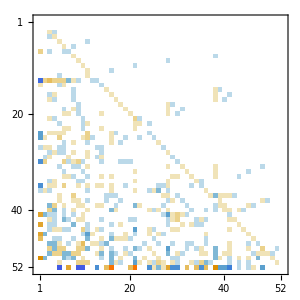
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{MatrixPlot[matrix1-Transpose[matrix2],ImageSize->300],MatrixPlot[matrix2,ImageSize->300],MatrixPlot[matrix1,ImageSize->300]}
```

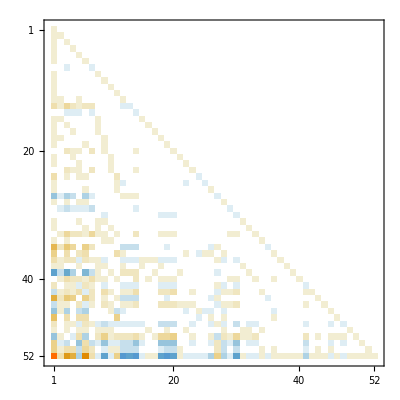

```mathematica
Inverse[matrix1]//MatrixPlot
```

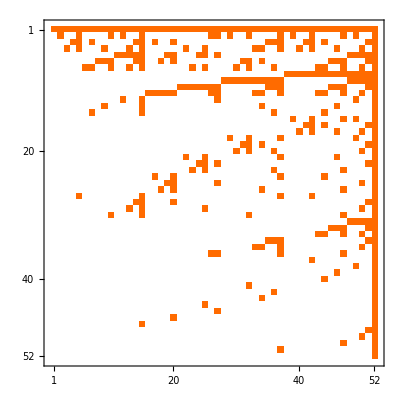

```mathematica
Inverse[matrix2]//MatrixPlot
```

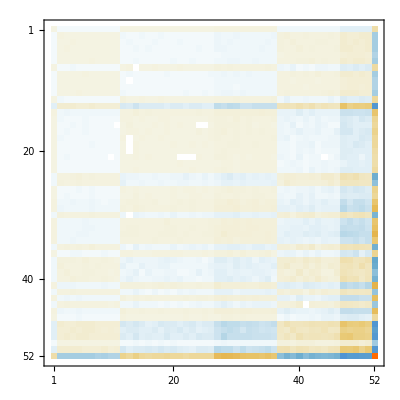
-Graphics-False

```mathematica
With[{mat=matrix1.matrix2},Labeled[MatrixPlot[mat],mat==Transpose[mat]]]
```

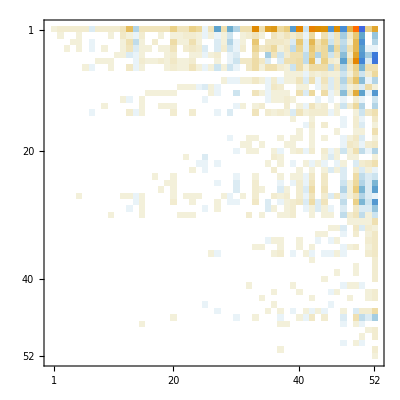

```mathematica
Inverse[matrix2].Inverse[Transpose[matrix1]
]//MatrixPlot
```

```mathematica
SymmetricMatrixQ
```

SymmetricMatrixQ

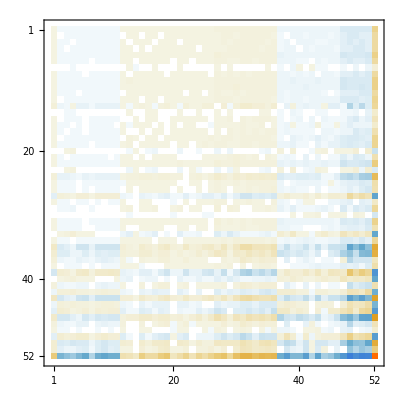

```mathematica
Table[Indexed[x,{i,j}],{i,1,52},{j,1,52}]/.First[Solve[matrix1.Table[Indexed[x,{i,j}],{i,1,52},{j,1,52}]==matrix2,Flatten[Table[Indexed[x,{i,j}],{i,1,52},{j,1,52}]]]]//MatrixPlot
```

```mathematica
matrix1.GenCoeff[allGraphs5[0,"colofourgenerator"]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}

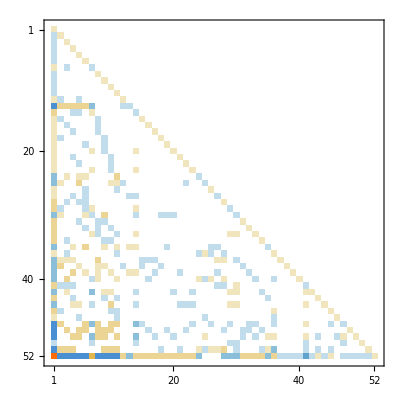

```mathematica
Table[GenCoeff[allGraphs5[k,"colofourgenerator"]],{k,allGraphs5GeneratorAtomKeys}].matrix1//MatrixPlot
```

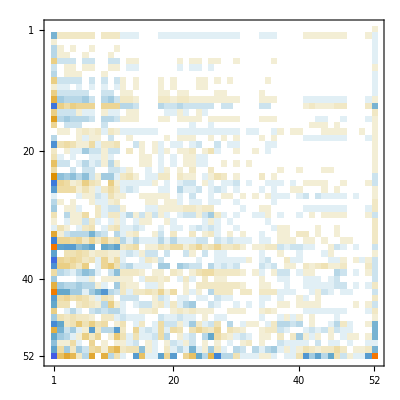

```mathematica
matrix1.Table[GenCoeff[allGraphs5[k,"colofourgenerator"]],{k,allGraphs5FakeAtomKeys}]//MatrixPlot
```

```mathematica
EmptyCoeff[allGraphs5[alfa1Key,"colofourrealnull"]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,-1,0,0,0,0,-1,0,0,0,2}